```mathematica
Exit[]
```

```mathematica
$Assumptions=μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
ost == σ √t; mpr==(μ-r)/σ^2;
xx[W_,mpr_,ost_]:=Exp[ ost W+(mpr-1/2)ost^2];
Δ[k_]:=1/2(1+Erf[(-Log[k]+ost^2/2)/ost])-1//N
Δ[0.]=0;
```

```mathematica
γ=.1;mpr=0.1;ost=.01;
NIntegrate[xx[w,mpr,ost]Exp[-w^2/2],{w,-∞,∞}]/√(2π)-Exp[mpr ost^2]

pr[f_]:=Log[NIntegrate[Exp[-γ f[xx[w,mpr,ost]]-w^2/2],{w,-∞,∞}]/√(2π)]/-γ;
opt2[f_]:=NIntegrate[Exp[-γ f[xx[w,mpr,ost]]-w^2/2](xx[w,mpr,ost]-1),{w,-∞,∞}];
opt[f_]:=Min[.1,Max[-.1,opt2[f]]]

h[a_]:=a(#-1)&
put[k_,a_]:=h[a][#]-Max[0,k-#]&;
```

-6.54587×10^-13

```mathematica
γ=.1;mpr=0.1;ost=1;arb=Quiet[FindRoot[opt2[h[b]]==0,{b,0,10}][[1,2]]]
hedge[k_]:=If[opt2[put[k,0]]≤ 0,0,FindRoot[opt2[put[k,a]]==0,{a,0,10}][[1,2]]]

plot[kl_]:=Module[{x=Quiet[hedge[#]]&/@kl,y,i=1},
y=Max[x];
Show[ParallelTable[With[{j=i++},
Plot[pr[put[k,a]]-put[k,a][1],{a,0,3 y},
PlotStyle->{ColorData[1,"ColorList"][[j]]}
]],{k,kl}],
PlotRange->All,
Epilog->Flatten[{Directive[{Dashed,Red}],
Table[
{Point[{x[[i]],0}],
Point[{x[[i]],pr[put[kl[[i]],x[[i]]]]-put[kl[[i]],x[[i]]][1]}]}
,{i,Length[kl]}]}]
]]
```

0.621583

```mathematica
$Assumptions=k≥ 0&&b>0;
```

```mathematica
ost=.;mpr=.
```

```mathematica
D[f[a,w,b],a]
```

ⅇ^(-a (-1+ⅇ^((-1/2+mpr) ost^2+ost w-b w^2))-w^2/2) (1-ⅇ^((-1/2+mpr) ost^2+ost w-b w^2))

```mathematica
f[a_,w_,b_]:=Exp[-a (ⅇ^((mpr -1/2)ost^2+ ost w-b w^2)-1)-w^2/2]
df[a_,w_,b_]:=ⅇ^(-a (-1+ⅇ^((-1/2+mpr) ost^2+ost w-b w^2))-w^2/2) (1-ⅇ^((-1/2+mpr) ost^2+ost w-b w^2))
g[a_,b_]:=NIntegrate[f[a,w,0],{w,-∞,b}]
dg[a_,b_]:=NIntegrate[df[a,w,0],{w,-∞,b}]
```

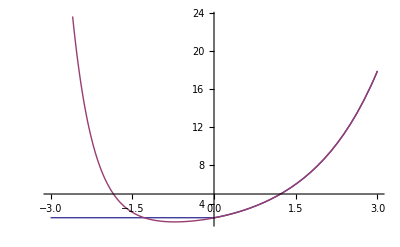

```mathematica
b=2.4;o=-3;p=3;Plot[{g[Max[0,a],∞],g[a,b]},{a,o,p}]
```

NIntegrate::inumri: The integrand ⅇ^2.99988\ (-1 + ⅇ^-1. + w) - w^2/2 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{29., 30.}}.

NIntegrate::inumri: The integrand ⅇ^2.87743\ (-1 + ⅇ^-1. + w) - w^2/2 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{29., 30.}}.

General::stop: Further output of NIntegrate :: inumri will be suppressed during this calculation.

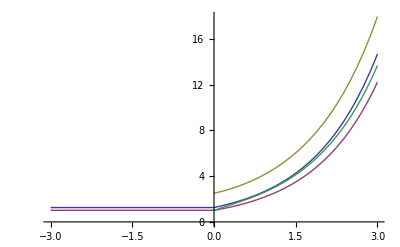

```mathematica
b=30;o=-3;p=3;Plot[{g[Max[0,a],0],dg[Max[0,a],0],g[a,b],dg[a,b]},{a,o,p}]
```

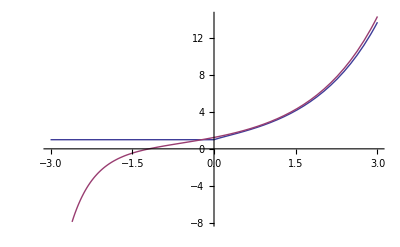

```mathematica
b=.1;o=-3;p=3;Plot[{dg[Max[0,a],0],dg[a,b]},{a,o,p}]
```

```mathematica
h[b_]:=Quiet[FindRoot[dg[a,b]==0,{a,-5,5}][[1,2]]]
```

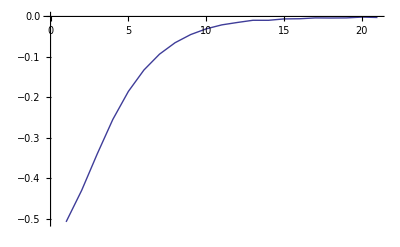

```mathematica
ListLinePlot[Table[h[1/n/2],{n,10,30}]]
```

```mathematica
fcs=Quiet[Table[fc2[n],{n,650}]];
```

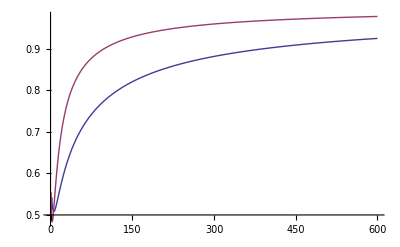

```mathematica
ListLinePlot[Transpose[Table[{Abs[fcs[[n]]]^(1/n),Abs[fcs[[n+1]]/fcs[[n]]]},{n,1,600}]]]
```